```mathematica
yyy+1/x yy-2y=x^2;
x0=0.5;
yy0=-0.5;
y0=-1;
```

6

{0.5,0.6,0.7,0.8,0.9,1.}

{{},0.05,0.265847,0.654618,1.25956,2.12806}

{{},1.5,3.02825,4.97162,7.3688,10.2632}

Print

6

{0.5,0.6,0.7,0.8,0.9,1.}

{{},-2.95,-2.9557,-3.02037,-3.15715,-3.37976}

{{},0.166667,-0.35656,-1.01039,-1.79889,-2.72956}

{{0.5,0,0.5},{0.6,0.1,1.65847},{0.7,0.334336,3.20282},{0.8,0.743058,5.16497},{0.9,1.36975,7.58313},{1.,2.26207,10.5003}}

{{0.5,-1.85896,0.5},{0.6,-1.80027,0.698768},{0.7,-1.71879,0.961861},{0.8,-1.60746,1.30182},{0.9,-1.45797,1.73083},{1.,-1.26082,2.26082}}

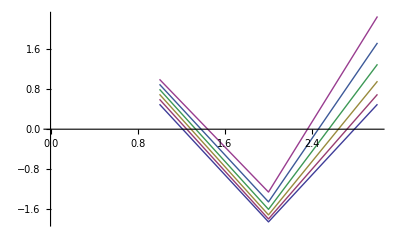

```mathematica
(*n=(b-a)/h+1;*)
solve[f1_,f2_, y0_,z0_] :=(
a=0.5;
b=1;
h = 0.1;
X=Range[a,b,h];
n=Length[X];
Print[n];
Print[X];
Y=Table[{},{n}];
Z=Table[{},{n}];
Y2=Table[{},{n}];
Z2=Table[{},{n}];
Y2[[1]]=y0;
Z2[[1]]=z0;
For[i=2,i≤n,i++,
Y[[i]]=Y2[[i-1]]+h*f1[X[[i-1]],Y2[[i-1]],Z2[[i-1]]];
Z[[i]]=Z2[[i-1]]+h*f2[X[[i-1]],Y2[[i-1]],Z2[[i-1]]];
Y2[[i]]=Y2[[i-1]]+h*(f1[X[[i-1]],Y2[[i-1]],Z2[[i-1]]]+f1[X[[i]],Y[[i]],Z[[i]]])/2;
Z2[[i]]=Z2[[i-1]]+h*(f2[X[[i-1]],Y2[[i-1]],Z2[[i-1]]]+f2[X[[i]],Y2[[i]],Z[[i]]])/2;
];
Print[Y];
Print[Z];
dots=Table[{},{n}];
For[i=1,i≤n,i++,
dots[[i]]={X[[i]],Y2[[i]],Z2[[i]]};
];
(*ListLinePlot[dots]*)
Return[dots];
);

f1[x_,y_,z_]:=z;(*y'*)
f2[x_,y_,z_]:=8+2/x z + 4/(x^2+2)y; (*z'*)
(*f3[x_,y_,z_]:=2/x z + 4/(x^2+2)y; *)
t0 = 0;
t1 = -3;
y0=t0;
z0=0.5;
dots1 = solve[f1,f2,y0,z0];
Print
y0=t1;
z0=0.5;
dots2 = solve[f1,f3,y0,z0];
Print[dots1];
c = (1 - dots1[[6,2]] - dots1[[6,3]])/(dots2[[6,2]] - dots1[[6,2]] + dots2[[6,3]] - dots1[[6,3]]);
dots = (1 - c) dots1 + c * dots2;
Print[dots];
ListLinePlot[dots]
```